```mathematica
ClearAll["Global`*"];
dndm[m_]:=Piecewise[{{A m^-1.3,m>0.08&&m<0.5},{A 0.5 m^-2.3,m≥0.5&&m<100}}]
(*dndm[m_]:=Piecewise[{{A m^-2.35,m>0.08&&m<100}}]*)
int=Integrate[dndm[m],m]
n[m_]:=Evaluate[Piecewise[int[[1]]]]
Print["n[x]="]
n[x]
dndx=D[n[x],x];
dndxfun[x_]:=Evaluate[Piecewise[dndx[[1]]]]
dndlogx[x_]:=Piecewise[Evaluate[Table[{Simplify[i[[1]]*x*Log[10]],i[[2]]},{i,dndxfun[x][[1]]}]]]
Print["dn/dLog10[x]="]
dndlogx[x]
```

Piecewise[{{0., m≤0.08}, {7.11135 A-(3.33333 A)/m^(3/10), 0.08<m≤0.5}, {3.95456 A-(0.384615 A)/m^(13/10), 0.5<m≤100.}, {3.9536 A, True}}]

n[x]=

Piecewise[{{0., x≤0.08}, {7.11135 A-(3.33333 A)/x^(3/10), 0.08<x≤0.5}, {3.95456 A-(0.384615 A)/x^(13/10), 0.5<x≤100.}, {0, True}}]

dn/dLog10[x]=

Piecewise[{{0, x<2/25}, {(2.30259 A)/x^(3/10), 2/25<x<1/2}, {(1.15129 A)/x^(13/10), 1/2<x<100}, {0, True}}]

```mathematica
Normalization
```

```mathematica
n[100]
```

3.9536 A

```mathematica
frac[x_]:=Piecewise[Table[{Evaluate[Simplify[i[[1]]/n[100]]],i[[2]]},{i,n[x][[1]]}]]
frac[x]
Assuming[0<x<1,Table[Simplify[Solve[frac[y][[1]][[inte]][[1]]==x,y]],{inte,2,3}]]
(*frac[x_]:=Piecewise[{{n[x][[2]][[1]]/n[100][[3]][[1]],n[x][[2]][[2]]},{n[x][[3]][[1]]/n[100][[3]][[1]]}}]
frac[x]*)
```

Piecewise[{{0., x≤0.08}, {1.7987-0.843114/x^(3/10), 0.08<x≤0.5}, {1.00024-0.0972824/x^(13/10), 0.5<x≤100.}, {0, True}}]

{{{y→-0.566179/((1.7987-1. x)^(1/3) (-5.81939+9.70599 x-5.39611 x^2+x^3))}},{{y→0.166558/(1.00024-1. x)^(10/13)}}}

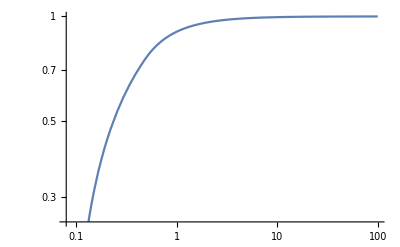

0.760707

```mathematica
LogLogPlot[frac[x]/.x->xx,{xx,0.08,100}]
frac[x]/.x->0.5
```

```mathematica
theory[x_]:=((1-x)*min^(a+1)+x*max^(a+1))^(1/(a+1))/.{min->0.08,max->100,a->-2.35}
Simplify[theory[x]]
```

1/(30.2572-30.2552 x)^0.740741

```mathematica
Assuming[a>0,Solve[a x==2,x]]
```

{{x→2/a}}